### The Kuramoto - Sivashinky equation with viscous damping: spatiotemporal evolution

The KS nonlinear PDE that models spatiotemporal evolution of situations such as flame fronts, flows of liquid films down inclines... may be solved numerically as an initial value problem with periodic spatial boundary conditions.

In the model considered below, there is a balance between capillary (fourth order term), advection (nonlinear term at the end) and destabilizing term (second order term) leading to the evolution that may turn unstable depending on the parameter (λ,⋁) ratios.

```mathematica
(∂u(t,x))/(∂t)+u(t,x) (∂u(t,x))/(∂x)+ (∂^2 u(t,x))/(∂x^2)+δ(∂^3 u(t,x))/(∂x^3)+(∂^4 u(t,x))/(∂x^4)==0
```

```mathematica
met0={{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","DifferenceOrder"->"Pseudospectral"},Method->"LSODA"},MaxSteps->Infinity};
```

```mathematica
met={MaxSteps->∞,Method->{"MethodOfLines","Method"->"LSODA","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->100,"DifferenceOrder"->5}},AccuracyGoal->∞};
```

```mathematica
λ=3;a=1;x0=20.;ν=1.;tmax=2500.;
δ=.34;
ks=D[u[t, x], {t}] + u[t, x]*D[u[t, x], {x}] + D[u[t, x], {x, 2}] + δ*D[u[t, x], {x, 3}] + D[u[t, x], {x, 4}] ;

sol=NDSolveValue[{ks==0,u[0,x]==ⅇ^(-(x-a)^2)+ⅇ^(-(x+a)^2) ,u[t,-x0]==u[t,x0]},u,{t,0,tmax},{x,-x0,x0}]
```

InterpolatingFunction[{{0., 2500.}, {…, -20., 20., …}}, <>]

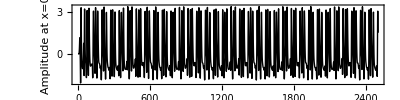

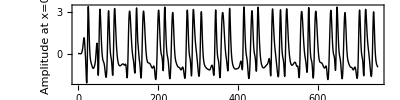

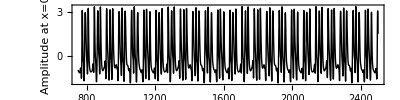

```mathematica
Plot[sol[t,-x0],{t,0,tmax},Frame->True, FrameStyle->Black,PlotStyle->{Thick,Black},BaseStyle->{FontSize->14},FrameLabel->{"Time","Amplitude at x=0"},AspectRatio->1/4]

nstart1=0.;
nend1=0.3 tmax;
nstart2=nend1;

Plot[sol[t,-x0],{t,nstart1,nend1},Frame->True, FrameStyle->Black,PlotStyle->{Thick,Black},BaseStyle->{FontSize->14},FrameLabel->{"Time","Amplitude at x=0"},AspectRatio->1/4]

Plot[sol[t,-x0],{t,nstart2,tmax},Frame->True, FrameStyle->Black,PlotStyle->{Thick,Black},BaseStyle->{FontSize->14},FrameLabel->{"Time","Amplitude at x=0"},AspectRatio->1/4]
(*datatime=Table[sol[t,-x0],{t,0,tmax,tmax/4000}];
ListPlot[datatime,Joined->True,Frame->True,PlotStyle->{Thick,Black},BaseStyle->{FontSize->22,Bold},ImageSize->600,Frame->True,FrameLabel->{"T (time)","Wave profile \n u(T,X)"}];*)
```

```mathematica
tval=tmax;
ndivs=400;
dissipative=Table[D[sol[t,xx],{xx,4}]/.xx->0,{t,0,tval,tval/ndivs}];
nonlinear=Table[sol[t,xx]D[sol[t,xx],xx]/.xx->0,{t,0,tval,tval/ndivs}];
dispersive=Table[δ D[sol[t,xx],{xx,3}]/.xx->0,{t,0,tval,tval/ndivs}];
```

```mathematica
err=Table[D[sol[tt, xx], {tt}] + sol[tt, xx]*D[sol[tt, xx], {xx}] + D[sol[tt, xx], {xx, 2}] + δ*D[sol[tt, xx], {xx, 3}] + D[sol[tt, xx], {xx, 4}]/.{xx->0,tt->τ} ,{τ,0,tval,tval/ndivs}];
```

```mathematica
err//Dimensions
```

{401}

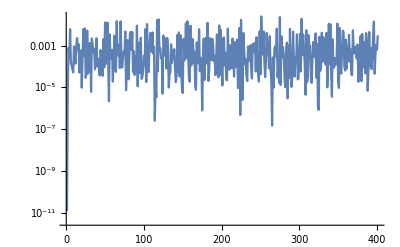

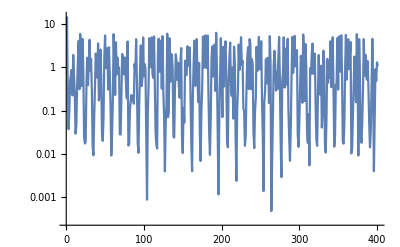

```mathematica
ListLogPlot[Abs[err],Joined->True]
ListLogPlot[Abs[dissipative-dispersive],Joined->True]
```

Strength of dissipative vs nonlinear effects

```mathematica
Plot[
{Abs[sol[t,xx]D[sol[t,xx],xx]]/.xx->0,
Abs[D[sol[t,xx],{xx,4}]]/.xx->0
},{t,0,tmax},PlotLegends->{"Nonlinear","Dissipative"},MaxRecursion->1]
```

```mathematica
dTable=Table[D[sol[t,xx],{xx,4}]/.xx->0,{t,0,tmax,tmax/4000}];
nTable=Table[sol[t,xx]D[sol[t,xx],xx]/.xx->0,{t,0,tmax,tmax/4000}];
```

```mathematica
normTable=Drop[Table[
Norm[dTable[[i]]-nTable[[i]],2]
,{i,1,4000,1}],1];
```

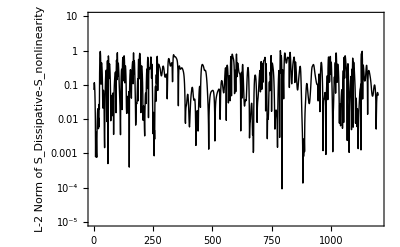

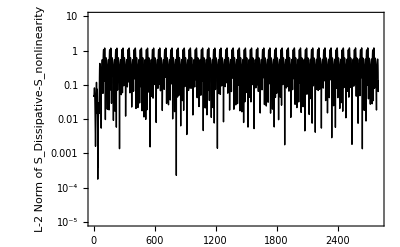

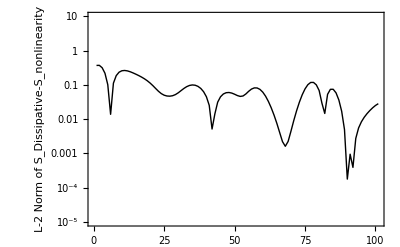

```mathematica
startPoint=1;endPoint=1200;
ListLogPlot[normTable[[startPoint;;endPoint]],Joined->True,Frame->True,PlotStyle->{Thick,Black},PlotRange->{All,{10^-5,10}},BaseStyle->{FontSize->14},FrameStyle->Black,FrameLabel->{"","L-2 Norm of \n S_Dissipative-S_nonlinearity"}]
startPoint=1200;endPoint=3999;
ListLogPlot[normTable[[startPoint;;endPoint]],Joined->True,Frame->True,PlotStyle->{Thick,Black},PlotRange->{All,{10^-5,10}},BaseStyle->{FontSize->14},FrameStyle->Black,FrameLabel->{"","L-2 Norm of \n S_Dissipative-S_nonlinearity"}]

startPoint=1150;endPoint=150;
ListLogPlot[normTable[[startPoint;;endPoint]],Joined->True,Frame->True,PlotStyle->{Thick,Black},PlotRange->{All,{10^-5,10}},BaseStyle->{FontSize->14},FrameStyle->Black,FrameLabel->{"","L-2 Norm of \n S_Dissipative-S_nonlinearity"}]
```

Starting with an initial condition that is u(0,x) = ⅇ^(-(x-a)^2)+ⅇ^(-(x+a)^2), the evolution shows a combination of ordered and chaotic states.

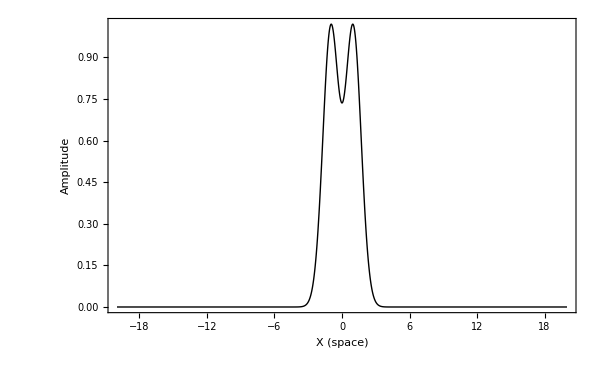

-Graphics3D-

```mathematica
initialCond=Plot[ⅇ^(-(x-a)^2)+ⅇ^(-(x+a)^2),{x,-20,20},PlotRange->All,PlotStyle->{Thick,Black},BaseStyle->{FontSize->22,Bold},ImageSize->600,Frame->True,FrameLabel->{"X (space)","Amplitude","INITIAL CONDITION"}]
p3d=Plot3D[sol[x,y],{x,0.,tmax},{y,-x0,x0},MaxRecursion->1,Mesh->None,ColorFunction->ColorData["Rainbow"],PlotRange->Full,PlotPoints->100,BaseStyle->{FontSize->15},AxesLabel->{"T","  X","Wave profile,\n u(T,X)"},ImageSize->600,PlotLabel->"Evolution of initial condition \nper the Kuramoto-Sivashinky equation"]
```

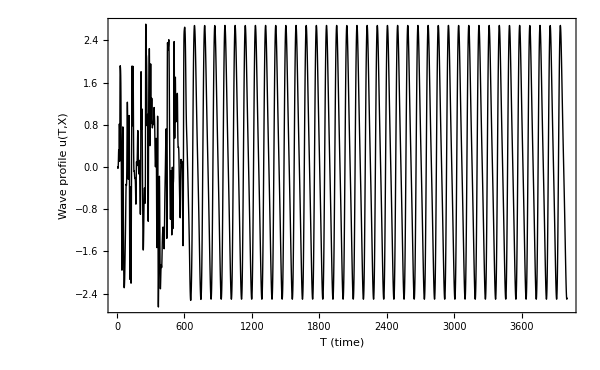

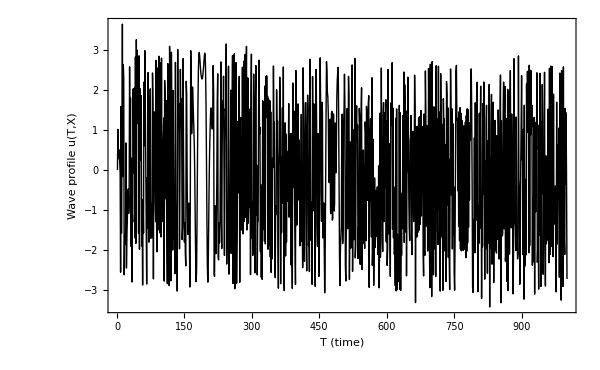

```mathematica
datatime=Table[sol[t,-x0],{t,0,tmax,tmax/4000}];
ListPlot[datatime,Joined->True,Frame->True,PlotStyle->{Thick,Black},BaseStyle->{FontSize->22,Bold},ImageSize->600,Frame->True,FrameLabel->{"T (time)","Wave profile \n u(T,X)"}]
```

```mathematica
tsol=Table[sol[tval,x],{x,-x0,x0},{tval,0,tmax,tmax/400}];
tsolx0=Table[sol[tval,0],{tval,0,tmax,tmax/1000}];
```

/home/dnaneet/Research_4.0/RQA/kuramoto_sivashinksy/ks_lambda-0x5_a-1x0_nu-1x0.dat

/home/dnaneet/Research_4.0/RQA/kuramoto_sivashinksy/_x0_ks_lambda-0x5_a-1x0_nu-1x0.dat

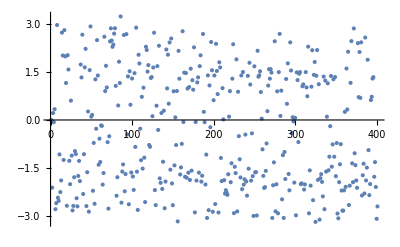

```mathematica
Export["/home/dnaneet/Research_4.0/RQA/kuramoto_sivashinksy/ks_lambda-0x5_a-1x0_nu-1x0.dat",tsol]
Export["/home/dnaneet/Research_4.0/RQA/kuramoto_sivashinksy/_x0_ks_lambda-0x5_a-1x0_nu-1x0.dat",datatime]
```

```mathematica
Manipulate[Plot[sol[tval,x],{x,-x0,x0},PlotRange->{{-x0,x0},{-4,4}}],{tval,0,tmax,tmax/100}]
```

### Reference

Alekseenko, Sergeĭ Vladimirovich et al., (1994) Wave flow of liquid films. New York : Begell House.